```mathematica
data=ReadList[NotebookDirectory[]<>"/ar-lab01-results-standard-K50-48nodes.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
fitData={#2,#7}&@@@data;
```

```mathematica
K=50;
nn=3600;
model=NonlinearModelFit[fitData,K((nn^2/p)t+2nn s),{t,s},p]
```

FittedModel[50 (0.0543493+0.521939/p)]

```mathematica
Show[
	ListPlot[fitData,PlotStyle->PointSize[0.008],AxesLabel->{"Processors","Total time"}, LabelStyle->Larger],
	Plot[model[x],{x,0,48},PlotStyle->Red],
	Frame->True
]
```

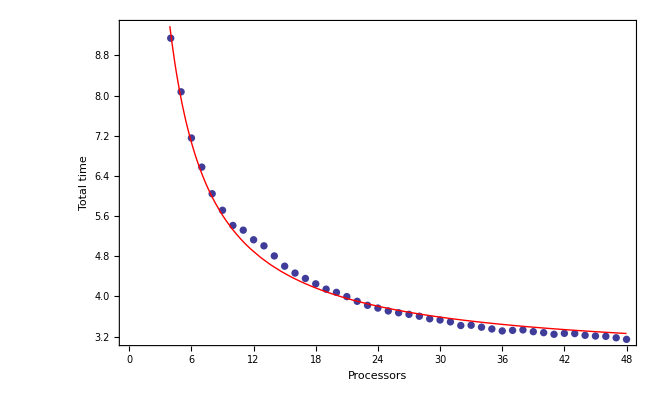

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
t | 4.02731×10^-8 | 1.66082×10^-10 | 242.489 | 4.05637×10^-73
s | 7.54851×10^-6 | 5.49933×10^-8 | 137.262 | 9.12876×10^-62